# Práctica 2 Autómatas Celulares

## Autores: Aitana Menárguez Box e Iñaki Diez Lambies

## Parte 1

```mathematica
AC[des_,regla_, t_]:=Module[{lRegla,res, i,aux},
lRegla = listaRegla[regla];
res = {};
aux = des; 
AppendTo[res,aux];
For[i=1,i≤t,i++,
aux = siguienteDes[aux,lRegla];
AppendTo[res,aux];
];
ArrayPlot[res]
]
```

```mathematica
siguienteDes[des_,regla_]:=Module[{nDes,n,t,q,i},
n = Length[des];
t=Cases[regla,{des[[n]],des[[1]],des[[2]],_}];
q= Flatten[t][[4]];
nDes = {};
AppendTo[nDes,q];
For[i=2,i<Length[des],i++,
t=Cases[regla,{des[[i-1]],des[[i]],des[[i+1]],_}]; 
q= Flatten[t][[4]];
AppendTo[nDes,q];
];
t=Cases[regla,{des[[n-1]],des[[n]],des[[1]],_}]; 
q= Flatten[t][[4]];
AppendTo[nDes,q];
Return[nDes];
]
```

```mathematica
listaRegla[n_]:=Module[{b,l,c,d,r,div,i},
b={}; 
l = {{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}; 
c = 0; 
d = n; 

While[ d >= 2 , 
div = QuotientRemainder[d,2];
r = div[[2]]; 
AppendTo[b, r];
d = div[[1]];
];
AppendTo[b, d]; 
b = PadRight[b,8]; 
For[i=1,i≤8,i++,
AppendTo[l[[i]],b[[i]]] 
];
Return [l];
]
```

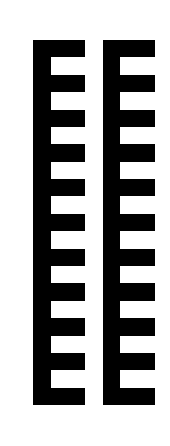

```mathematica
AC[{0,1,1,1,0,1,1,1},29, 20]
```